# Homework 3: Condensed Matter Core

## 1. Chern number and edge states for a two-band model

### c)

```mathematica
d[kx_,ky_,m_]:={Sin[kx],Sin[ky],Cos[kx]+Cos[ky]+m};
hatd[kx_,ky_,m_]:=d[kx,ky,m]/Norm[d[kx,ky,m]];
numint=Table[1/(4π)NIntegrate[hatd[kx,ky,m].(D[hatd[kx,ky,m],kx]×D[hatd[kx,ky,m],ky]),{kx,-π,π},{ky,-π,π}],{m,-5,5,0.2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.30243×10^-17 and 2.00697×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70355×10^-17 and 2.4307×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.54534×10^-17 and 2.78077×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-5.01532×10^-18,1.35564×10^-18,-2.82129×10^-18,4.78942×10^-19,7.01656×10^-18,6.21364×10^-18,-4.18017×10^-18,9.92198×10^-20,1.02186×10^-18,3.27981×10^-18,6.2832×10^-18,4.36136×10^-18,-7.21155×10^-17,-1.88308×10^-10,1.80472×10^-16,0.5,1.,1.,1.,1.,1.,1.,1.,1.,1.,6.72049×10^-12,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-0.5,-4.18333×10^-16,2.97179×10^-17,5.56158×10^-17,-8.06614×10^-17,-2.95558×10^-17,5.76875×10^-18,-2.76405×10^-17,-6.31016×10^-18,-4.458×10^-18,-5.12276×10^-18,1.76439×10^-18,-3.84996×10^-18,-1.7687×10^-18,-4.60799×10^-18,-7.55364×10^-18}

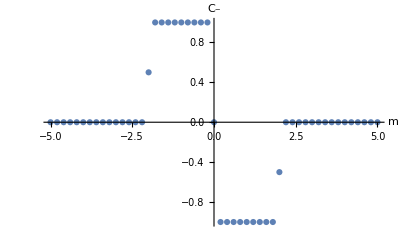

```mathematica
ListPlot[Transpose[{Range[-5,5,0.2],numint}],AxesLabel->{m,SubMinus[C]}]
```

### f)

```mathematica
m=-1.5;
lx=40;
ly=40;
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
m0={{0,0},{0,0}};
```

```mathematica
fM[ky_,x1_,x2_]:=Piecewise[{{Sin[ky]σy+(m+Cos[ky])σz, x1==x2}, {(σz-ⅈ σx)/2, x2==x1+1}, {(σz+ⅈ σx)/2, x2==x1-1}, {m0, True}}] 
matM[ky_]:=Table[fM[ky,Ceiling[i1/2],Ceiling[i2/2]][[Mod[i1,2,1],Mod[i2,2,1]]],{i1,1,2lx},{i2,1,2ly}]
```

```mathematica
numdiag=Table[Eigenvalues[N[matM[ky]]],{ky,-π,π,(2π)/ly}];
```

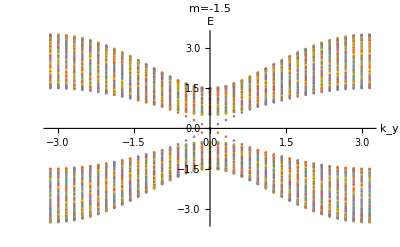

```mathematica
ListPlot[Table[Transpose[{Range[-π,π,(2π)/ly],numdiag[[All,i]]}],{i,1,80}],AxesLabel->{Subscript[k, y],"E"},PlotLabel->"m=-1.5"]
```

### h)

```mathematica
m=-5;
```

```mathematica
fM[ky_,x1_,x2_]:=Piecewise[{{Sin[ky]σy+(m+Cos[ky])σz, x1==x2}, {(σz-ⅈ σx)/2, x2==x1+1}, {(σz+ⅈ σx)/2, x2==x1-1}, {m0, True}}] 
matM[ky_]:=Table[fM[ky,Ceiling[i1/2],Ceiling[i2/2]][[Mod[i1,2,1],Mod[i2,2,1]]],{i1,1,2lx},{i2,1,2ly}]
```

```mathematica
numdiag=Table[Eigenvalues[N[matM[ky]]],{ky,-π,π,(2π)/ly}];
```

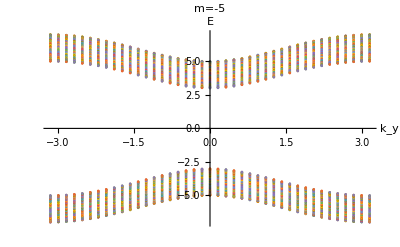

```mathematica
ListPlot[Table[Transpose[{Range[-π,π,(2π)/ly],numdiag[[All,i]]}],{i,1,80}],AxesLabel->{Subscript[k, y],"E"},PlotLabel->"m=-5"]
```